# Exercise 6.8

(c) The derivative of f(n) with respect to n to get the local stability of the continuous time differential equation, which is defined as r.

```mathematica
D[α P (1 - P) - σ P, P]
```

(1-P) α-P α-σ

(d) The global stability of P equilibria using a graphical technique.

(1-P) P α-P σ

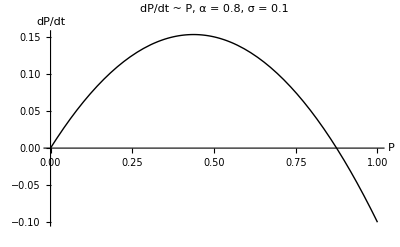

```mathematica
f = α P (1 - P) - σ P
Plot[f/.α-> 0.8/.σ -> 0.1, {P, 0, 1},
PlotTheme->"Classic",
PlotStyle-> {Black},
AxesLabel->{"P", "dP/dt"},
PlotLabel-> "dP/dt ~ P, α = 0.8, σ = 0.1"]
```

```mathematica
Export["/home/pratik/projects/courseMathModels/figChap6.8d.eps",%66,"EPS"]
```

/home/pratik/projects/courseMathModels/figChap6.8d.eps

(e) General solution for the model.

```mathematica
iP = Integrate[1/(α P (1 - P) - σ P), P]
```

```mathematica
-(-Log[P]+Log[(-1+P) α+σ])/(α-σ)
FullSimplify[iP]
```

-(-Log[P]+Log[(-1+P) α+σ])/(α-σ)

(Log[P]-Log[(-1+P) α+σ])/(α-σ)

```mathematica
eq2 = iP == t + c;
```

```mathematica
FullSimplify[Solve[eq2, P]]
```

{{P→(ⅇ^((c+t) α) (α-σ))/(-ⅇ^((c+t) σ)+ⅇ^((c+t) α) α)}}